```mathematica
Dynamic[{n,c,ds,Norm@f[xI,parsI,TR1+dT ds,uR1]}]
```

```mathematica
Norm@f[uR1,pars0,TR1,e7m1br01]
```

Norm[f[{1.23262,0.0977487,3.33489,0.386208,1.34163,3.27455,-1.02456,0.883589,3.29262,342,3.7454×10^-7,3.21606×10^-6,-6.32674×10^-7,-1.42122×10^-6,-3.52418×10^-6,-9.14503×10^-7,-1.18916×10^-7,3.6629×10^-7,6.72336×10^-10},2,{1}]]
 |  |  |  |

```mathematica
Graphics3D[{{Red,PointSize@Medium,Point[Partition[u1[[;;180]],3]]},{Blue,PointSize@Medium,Point[Partition[u0M,3]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[u1[[;;180]],3][[#]]&,idxD,{2}]]}},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[xI,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[xI,pars0,T1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[xI,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[u1,pars0,T1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[u1,pars0,T1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
Manipulate[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[uR1,pars0,TR1][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[uR1,pars0,TR1][t],3][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[uR1,pars0,TR1][t],3][[;;60]][[#]]&,idxD,{2}]]}}],{t,0,1,0.1}]
```

```mathematica
StringReplace[ToString@e7m1br01[[-1,1]],"."->""]
```

0541037

```mathematica
animation=Table[Graphics3D[{
{Red,PointSize@Medium,Point[Partition[flux[e7m1br01[[-1,2]],pars0,e7m1br01[[-1,1]]][t],3][[;;60]]]},{Gray,Line[Map[Partition[flux[e7m1br01[[-1,2]],pars0,e7m1br01[[-1,1]]][t],3][[;;60]][[#]]&,idxS,{2}]]},{Gray,Line[Map[Partition[flux[e7m1br01[[-1,2]],pars0,e7m1br01[[-1,1]]][t],3][[;;60]][[#]]&,idxD,{2}]]}},PlotRange->4,ImageSize->Large,Boxed->False],{t,0,1,1/50}];
```

```mathematica
Export[NotebookDirectory[]<>"E"<>ToString@l<>"-1-"<>StringReplace[ToString@e7m1br01[[-1,1]],"."->""]<>".gif",animation,"DisplayDurations"->1/25,"AnimationRepetitions"->∞]
```

C:\Users\Manuel\Dropbox\EquivariantDegree\FullereneC60\Mathematica\E7-1-0540901.gif

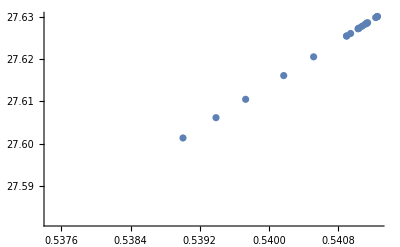

```mathematica
ListPlot[{#1,Norm@#2}&@@@e7m1br01]
```